```mathematica
SetDirectory@NotebookDirectory[];
robot=Import["Robot_banana.jpg","ImageWithExif",ImageSize->250];robot
```

-Graphics-

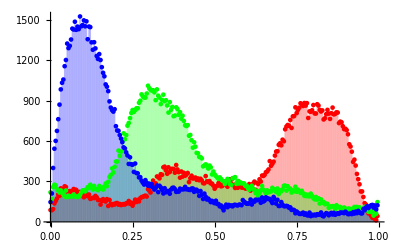

```mathematica
​ ImageLevels[robot];

ListPlot[ ImageLevels[robot],PlotStyle->{Red,Green,Blue},Filling->Axis]
```